From Lab 5: Nonlinear pendulum

{{ϕ→InterpolatingFunction[…]}}

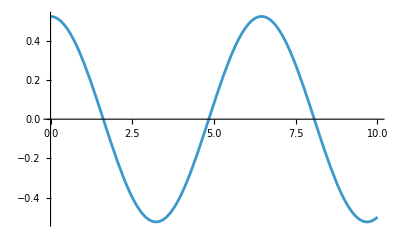

```mathematica
g = 9.81;
l = 10;
ω = Sqrt[g/l];

sol=NDSolve[{ϕ''[t]==-ω^2 Sin[ϕ[t]],ϕ'[0]==0,ϕ[0]==30 Degree},ϕ,{t,0,10}]
Plot[ϕ[x]/. sol,{x,0,10}]
```

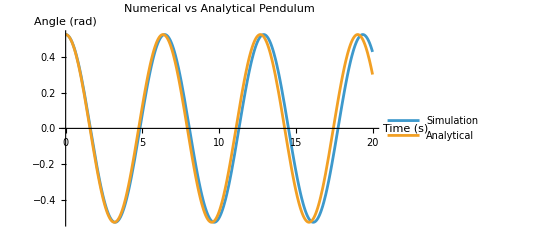

```mathematica
g=9.81;
l=10;
ω=Sqrt[g/l];
angle=30 Degree;

sol=NDSolve[{ϕ''[t]==-ω^2 Sin[ϕ[t]],ϕ'[0]==0,ϕ[0]==angle},ϕ,{t,0,20}];

analytical[t_]:=angle Cos[ω t];

Plot[Evaluate[{ϕ[t]/. First[sol],analytical[t]}],{t,0,20},PlotLegends->{"Simulation","Analytical"},AxesLabel->{"Time (s)","Angle (rad)"},PlotLabel->"Numerical vs Analytical Pendulum"]
```